```mathematica
ClearAll["Global`*"];
```

Revision history: 
2020-04-03: 	initial version
2020-04-06:	Added missing factor Ms to all expressions containing the fitted susceptbilities, which are χ/Ms.

Coordinate system
 -Graphics-

## Susceptibilities

Fitting the raw S21 data has to consider the corresponding susceptibility tensor components (taken from Habil MW Equation 2.7). For these equations the 3 direction is along the M equilibrium orientation and χ describes the orthogonal 1 and 2 components with the 2 direction always in-plane.

```mathematica
χinvoop=1/(μ0 γ)({{γ(μ0H0-μ0Meff)+ⅈ α ω, -ⅈ ω}, {ⅈ ω, γ(μ0H0-μ0Meff)+ⅈ α ω}});
```

```mathematica
χinvip=1/(μ0 γ)({{γ (μ0H0+μ0Meff)+ⅈ α ω, -ⅈ ω}, {ⅈ ω, γ μ0H0+ⅈ α ω}});
```

```mathematica
χOOP=Inverse[χinvoop]*Ms//FullSimplify;
```

```mathematica
χOOP*Det[χinvoop]/Ms//FullSimplify//MatrixForm
```

((γ μ0H0-γ μ0Meff+ⅈ α ω)/(γ μ0) | (ⅈ ω)/(γ μ0)
-(ⅈ ω)/(γ μ0) | (γ μ0H0-γ μ0Meff+ⅈ α ω)/(γ μ0))

```mathematica
χIP=Inverse[χinvip]*Ms//FullSimplify;
```

```mathematica
χIP*Det[χinvip]/Ms//FullSimplify//MatrixForm
```

((γ μ0H0+ⅈ α ω)/(γ μ0) | (ⅈ ω)/(γ μ0)
-(ⅈ ω)/(γ μ0) | (γ (μ0H0+μ0Meff)+ⅈ α ω)/(γ μ0))

We now switch to the xyz coordinate system shown above. The components that need to be used in fitting are the diagonal components of the corresponding susceptibilities (we have to be careful with choosing the correct component for the IP susceptibility). We always divide χ by Ms for the fits (in Labview, FTF) only. All other occurences of χ in equations are unitless. For the case of H along z, only the driving field along y can couple:

```mathematica
χfitZ=χOOP[[2,2]]/Ms
```

(γ μ0 (γ (μ0H0-μ0Meff)+ⅈ α ω))/(γ^2 (μ0H0-μ0Meff)^2+2 ⅈ α γ (μ0H0-μ0Meff) ω-(1+α^2) ω^2)

For H along y, only the OOP driving field can couple :

```mathematica
χfitY=χIP[[1,1]]/Ms
```

(γ μ0 (γ μ0H0+ⅈ α ω))/(γ^2 μ0H0 (μ0H0+μ0Meff)+ⅈ α γ (2 μ0H0+μ0Meff) ω-(1+α^2) ω^2)

For H along x, both IP and OOP driving fields can couple. Here ξ is the ratio between the coupling efficiency. ζ=1 is expected for an insulating ferromagnet, however in the presence of microwave shielding the IP and OOP driving fields may be shielded with different efficiency, resulting in ζ ≠1.

```mathematica
χfitX=(ζ χIP[[1,1]]+ χIP[[2,2]])/Ms//FullSimplify
```

(γ μ0 (γ (μ0H0+ζ μ0H0+μ0Meff)+ⅈ α (1+ζ) ω))/(γ^2 μ0H0 (μ0H0+μ0Meff)+ⅈ α γ (2 μ0H0+μ0Meff) ω-(1+α^2) ω^2)

## Fitting equations for Labview

In the following, we give the fit equations that should be copy + pasted into Labview

```mathematica
replacementrules={γ->gamma, μ0->mu0, α->alpha, μ0H0->mu0H0, ω->omega, μ0Meff->mu0Meff, ζ->ratio};
```

## Out-of-plane (H || z):

OOP real:

```mathematica
ToString[ComplexExpand[Re[χfitZ]]/.replacementrules//FullSimplify//FortranForm]
```

(gamma**2*mu0*(mu0H0 - mu0Meff)*(gamma**2*(mu0H0 - mu0Meff)**2 + (-1 + alpha**2)*omega**2))/(gamma**4*(mu0H0 - mu0Meff)**4 + 2*(-1 + alpha**2)*gamma**2*(mu0H0 - mu0Meff)**2*omega**2 + (1 + alpha**2)**2*omega**4)

OOP imaginary :

```mathematica
ToString[ComplexExpand[Im[χfitZ]]/.replacementrules//FullSimplify//FortranForm]
```

-((alpha*gamma*mu0*omega*(gamma**2*(mu0H0 - mu0Meff)**2 + (1 + alpha**2)*omega**2))/(gamma**4*(mu0H0 - mu0Meff)**4 + 2*(-1 + alpha**2)*gamma**2*(mu0H0 - mu0Meff)**2*omega**2 + (1 + alpha**2)**2*omega**4))

## In-plane (H orthogonal to CPW, H || y):

IP orthogonal real:

```mathematica
ToString[ComplexExpand[Re[χfitY]]/.replacementrules//FullSimplify//FortranForm]
```

(gamma**2*mu0*(gamma**2*mu0H0**2*(mu0H0 + mu0Meff) + ((-1 + alpha**2)*mu0H0 + alpha**2*mu0Meff)*omega**2))/(gamma**4*mu0H0**2*(mu0H0 + mu0Meff)**2 + gamma**2*(2*(-1 + alpha**2)*mu0H0**2 + 2*(-1 + alpha**2)*mu0H0*mu0Meff + alpha**2*mu0Meff**2)*omega**2 + (1 + alpha**2)**2*omega**4)

IP orthogonal imaginary :

```mathematica
ToString[ComplexExpand[Im[χfitY]]/.replacementrules//FullSimplify//FortranForm]
```

-((alpha*gamma*mu0*omega*(gamma**2*mu0H0**2 + (1 + alpha**2)*omega**2))/(gamma**4*mu0H0**2*(mu0H0 + mu0Meff)**2 + gamma**2*(2*(-1 + alpha**2)*mu0H0**2 + 2*(-1 + alpha**2)*mu0H0*mu0Meff + alpha**2*mu0Meff**2)*omega**2 + (1 + alpha**2)**2*omega**4))

## In-plane (H parallel to CPW, H || x):

IP parallel real:

```mathematica
ToString[ComplexExpand[Re[χfitX]]/.replacementrules//FullSimplify//FortranForm]
```

(gamma**2*mu0*(gamma**2*mu0H0*(mu0H0 + mu0Meff)*(mu0H0 + mu0Meff + mu0H0*ratio) + omega**2*((-1 + alpha**2)*mu0H0*(1 + ratio) + mu0Meff*(-1 + alpha**2*ratio))))/(gamma**4*mu0H0**2*(mu0H0 + mu0Meff)**2 + gamma**2*(2*(-1 + alpha**2)*mu0H0**2 + 2*(-1 + alpha**2)*mu0H0*mu0Meff + alpha**2*mu0Meff**2)*omega**2 + (1 + alpha**2)**2*omega**4)

IP parallel imaginary:

```mathematica
ToString[ComplexExpand[Im[χfitX]]/.replacementrules//FullSimplify//FortranForm]
```

-((alpha*gamma*mu0*omega*((1 + alpha**2)*omega**2*(1 + ratio) + gamma**2*((mu0H0 + mu0Meff)**2 + mu0H0**2*ratio)))/(gamma**4*mu0H0**2*(mu0H0 + mu0Meff)**2 + gamma**2*(2*(-1 + alpha**2)*mu0H0**2 + 2*(-1 + alpha**2)*mu0H0*mu0Meff + alpha**2*mu0Meff**2)*omega**2 + (1 + alpha**2)**2*omega**4))

## CPW sensitivity and dipolar inductance

We now turn to the evaluation of L0 and LNM, where we use the coordinate system indicated in the figure above

```mathematica
x0={1,0,0};
y0={0,1,0};
z0={0,0,1};
```

## Driving fields

The Karqvist model is used to describe the Oersted fields generated from the CPW

```mathematica
hyKF=I0/(2 w π)(ArcTan[(w/2+y)/z]+ArcTan[(w/2-y)/z]);
```

```mathematica
hzKF=I0/(4 w π)Log[((w/2+y)^2+z^2)/((w/2-y)^2+z^2)];
```

Same equations can be simplified by introducing parameters Ay and Az

```mathematica
hyK=I0/(2 w π)Ay;
```

```mathematica
hzK=I0/(4 w π)Az;
```

Where

Ay=(ArcTan[(w/2+y)/z]+ArcTan[(w/2-y)/z]) 
Az=Log[((w/2+y)^2+z^2)/((w/2-y)^2+z^2)]

The driving field vector is given by

```mathematica
h1={0,hy,hz};
```

And the unitless magnetic susceptibility in general is

```mathematica
χ=({{χxx, χxy, χxz}, {χyx, χyy, χyz}, {χzx, χzy, χzz}});
```

Resulting in the magnetization (linear response)

```mathematica
m=χ.h1;
```

## CPW sensitivity by reciprocity

We rely on principle of reciprocity. If the magnetic field of the CPW due to current I0 is given by H(y,z) = CH(y,z)*I0 with any function CH, then the inductance generated by a magnetic dipole moment is L=ϕ/I0 with flux ϕ=μ0 CH(y,z) m(y,z)

The general form of the inductance of sample with volume V is thus L0=μ0/I0∫CH *mⅆV=μ0/I0d l∫_(-∞)^∞ CH*mⅆy, where we assume that the film has small thickness d and length l, so we only have to integrate over y.

We define the sensitivity function

```mathematica
CH={0, hy/I0, hz/I0};
```

We now need to write down all terms in the form CH*m. For the Hx case all components of χ that contain an index x vanish. Furthermore, off-diagonal elements of χ have identical magnitude but opposite sign. We consider shielding (or amplification due to image currents) of the driving fields hy and hz by a factor ξ and also consider that the driving field hy might be shielded differently to the driving field hz by the factor ζ already introduced above.

```mathematica
mSensx=Collect[m.CH/.{χxx->0, χxy->0, χxz->0,χyx->0, χzx->0, χzy->-χyz,hy->ξ  hyK, hz->ξ ζ hzK},{χyy, χzz}]
```

(Ay^2 I0 ξ^2 χyy)/(4 π^2 w^2)+(Az^2 I0 ζ^2 ξ^2 χzz)/(16 π^2 w^2)

For the Hy case

```mathematica
mSensy=m.CH/.{χyx->0, χyy->0, χyz->0,χxy->0, χzy->0,  hy->ξ hyK, hz->ξ ζ hzK}
```

(Az^2 I0 ζ^2 ξ^2 χzz)/(16 π^2 w^2)

For the Hz case :

```mathematica
mSensz=m.CH/.{χzx->0, χzy->0, χzz->0,χxz->0, χyz->0, hy->ξ hyK, hz->ξ ζ hzK}
```

(Ay^2 I0 ξ^2 χyy)/(4 π^2 w^2)

## Inductances

For all these, integration needs to be done only over the terms Ay^2 and Az^2, as other terms do not depend on y. Furthermore, we assume uniform driving field along length and thickness of the ferromagnet, so that integration of length and thickness can be replaced by multiplication. We thus obtain the inductances  L0=μ0/I0∫CH *mⅆV=μ0/I0d l∫_(-∞)^∞ CH*mⅆy:

```mathematica
L0x=(μ0 l d)/I0 mSensx/.{Ay->Ayint, Az->Azint}//FullSimplify
```

(d l μ0 ξ^2 (4 Ayint^2 χyy+Azint^2 ζ^2 χzz))/(16 π^2 w^2)

```mathematica
L0y=(μ0 l d)/I0 mSensy/.{Ay->Ayint, Az->Azint}//FullSimplify
```

(Azint^2 d l ζ^2 μ0 ξ^2 χzz)/(16 π^2 w^2)

```mathematica
L0z=(μ0 l d)/I0 mSensz/.{Ay->Ayint, Az->Azint}//FullSimplify
```

(Ayint^2 d l μ0 ξ^2 χyy)/(4 π^2 w^2)

We can determine the factors Ayint and Azint numerically

```mathematica
AyEval[z_,w_]:=Quiet[NIntegrate[(ArcTan[(w/2+y)/z]+ArcTan[(w/2-y)/z])^2,{y,-∞,∞}]];
```

```mathematica
AzEval[z_,w_]:=Quiet[NIntegrate[(Log[((w/2+y)^2+z^2)/((w/2-y)^2+z^2)])^2,{y,-∞,∞}]];
```

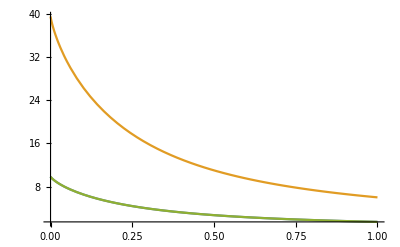

```mathematica
Plot[{AyEval[z,1],AzEval[z,1], AzEval[z,1]/4},{z,0,1}, PlotRange->All]
```

Evidently, AyEval=AzEval/4 for all values of z and in the limit of z -> 0 we find:

```mathematica
A0z=Integrate[(Log[(w/2+y)^2/(w/2-y)^2])^2,{y,-∞,∞}, Assumptions->w>0]
```

4 π^2 w

```mathematica
A0y=A0z/4
```

π^2 w

We first consider the case of direct contact of CPW and space (δ=0) and recover the known relation for L0 for H along z :

```mathematica
L0z/.Ayint^2->A0y
```

(d l μ0 ξ^2 χyy)/(4 w)

And find for H along x :

```mathematica
L0x/.{Ayint^2->A0y, Azint^2->A0z}//FullSimplify
```

(d l μ0 ξ^2 (χyy+ζ^2 χzz))/(4 w)

And for H along y:

```mathematica
L0y/.{Ayint^2->A0y, Azint^2->A0z}//FullSimplify
```

(d l ζ^2 μ0 ξ^2 χzz)/(4 w)

## Spacing loss

For the spacing loss (as shown above, identical for Hy and Hz) we take the usual approximation

```mathematica
η=2/π ArcTan[w/(2z)];
```

We now can plot the simplified spacing loss η together with the exact spacing loss as a function of z/w :

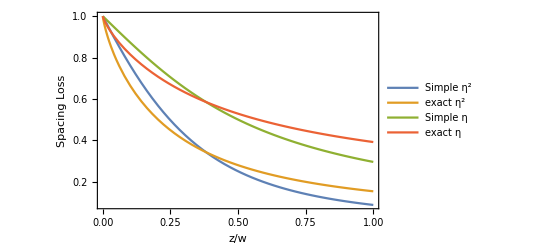

```mathematica
Plot[{ η^2/.{w->1},AyEval[z,1]/A0y/.{w->1}, η/.{w->1},√(AyEval[z,1]/A0y)/.{w->1}  },{z,0,1}, PlotRange->All, PlotLegends->{"Simple η^2", "exact η^2", "Simple η", "exact η"}, Frame->True, Axes->False, FrameLabel-> {"z/w","Spacing Loss"}]
```

We next try to find an analytical equation that approximates the spacing loss better than the simple η used so far:

```mathematica
ηexactlist=Join[{{0,1}},ParallelTable[{z,√(AyEval[z,1]/A0y)/.{w->1}},{z,0.01,10,0.01}]];
```

With κ = z/w we can let Mathematica find an analytical equation for the exact spacing loss

```mathematica
ηnew=FindFormula[ηexactlist,κ,PerformanceGoal->"Quality",RandomSeeding->666]
```

0.962365-1.56872 κ+2.05061 κ^2-1.71094 κ^3+0.915521 κ^4-0.322478 κ^5+0.0761812 κ^6-0.0121245 κ^7+0.00128146 κ^8-0.0000861519 κ^9+3.33281×10^-6 κ^10-5.64571×10^-8 κ^11

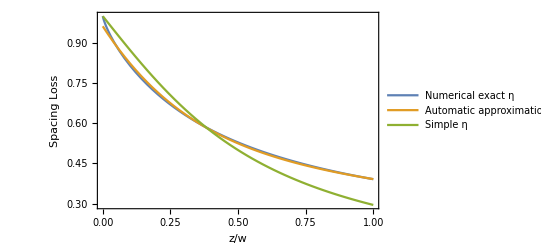

```mathematica
Plot[{√(AyEval[κ,1]/A0y)/.{w->1},ηnew, η/.{w->1, z->κ}},{κ,0,1},PlotLegends->{"Numerical exact η", "Automatic approximation of η", "Simple η"}, PlotRange->{All, {0,All}},Frame->True, Axes->False, FrameLabel-> {"z/w","Spacing Loss"}]
```

## Final equations for dipolar inductance

The simplification when using eta is reasonably good for our purposes, but exact η (ηnew) can also easily be used if necessary. The final equations to use for the dipolar inductance are thus

```mathematica
(*L0z/.{Ayint^2->A0y, Azint^2->A0z}//FullSimplify*)
```

L0x=(d l μ0 ξ^2(χIPyy+ζ^2 χIPzz))/(4 w)η^2=(d l μ0 Ms)/(4 w)ξ^2 χfitX η^2

L0y=(d l μ0 ξ^2 ζ^2 χIPzz)/(4 w)η^2=(d l μ0 Ms)/(4 w)ξ^2 ζ^2 χfitY η^2

L0z=(d l μ0 ξ^2 χOOPyy)/(4 w)η^2=(d l μ0 Ms)/(4 w)ξ^2 χfitZ η^2

with the fitting susceptibilities (Important note: These are actually χ/Ms!)

```mathematica
(*χfitZ//FullSimplify*)
```

χfitX=(γ μ0 (γ (μ0H0+ζ μ0H0+μ0Meff)+ⅈ α (1+ζ) ω))/(γ^2 μ0H0 (μ0H0+μ0Meff)+ⅈ α γ (2 μ0H0+μ0Meff) ω-(1+α^2) ω^2)

χfitY=(γ μ0 (γ μ0H0+ⅈ α ω))/(γ^2 μ0H0 (μ0H0+μ0Meff)+ⅈ α γ (2 μ0H0+μ0Meff) ω-(1+α^2) ω^2)

χfitZ=(γ μ0 (γ (μ0H0-μ0Meff)+ⅈ α ω))/(γ^2 (μ0H0-μ0Meff)^2+2 ⅈ α γ (μ0H0-μ0Meff) ω-(1+α^2) ω^2)

## SOT Inductances

We now turn to the additional inductance due to charge currents in the NM layer
-Graphics-

We first consider H applied along z and obtain the dynamic magnetization

```mathematica
mZ={ 1/Ms(χ.h1)[[1]], 1/Ms(χ.h1)[[2]],1}/.{χxz->0, χyz->0, χzz->0, χzx->0, χzy->0};
dtmZ={(ⅈ ω)/Ms(χ.h1)[[1]],(ⅈ ω)/Ms(χ.h1)[[2]],0}/.{χxz->0, χyz->0, χzz->0, χzx->0, χzy->0};
```

For H applied along x

```mathematica
mX={1,1/Ms(χ.h1)[[2]], 1/Ms(χ.h1)[[3]]}/.{χxx->0, χyx->0, χzx->0, χxy->0, χxz->0};
dtmX={0,(ⅈ ω)/Ms(χ.h1)[[2]],(ⅈ ω)/Ms(χ.h1)[[3]]}/.{χxx->0, χyx->0, χzx->0, χxy->0, χxz->0};
```

And finally for H applied along y

```mathematica
mY={ 1/Ms(χ.h1)[[1]],1, 1/Ms(χ.h1)[[3]]}/.{χxy->0, χyy->0, χzy->0, χyx->0, χyz->0};
dtmY={(ⅈ ω)/Ms(χ.h1)[[1]],0,(ⅈ ω)/Ms(χ.h1)[[3]]}/.{χxy-> 0, χyy->0, χzy->0, χyx->0, χyz->0};;
```

We can now calculate the currents from Eq 14 (Berger). First, we consider H applied along z and the appropriate symmetry of χ components

```mathematica
LNMZ=-L12/I0 x0.(z0 × dtmZ σFL-z0 ×( mZ× dtmZ) σDL)(ℏ w)/(2 e)/.{χxy->ⅈ χyy, hy->ξ I0/(2 w)η0}//Simplify
```

(L12 η0 ξ (σDL+ⅈ σFL) χyy ω ℏ)/(4 e Ms)

For H along x we use χIP=χzyIP(ⅈ ϵ | -1
1 | ⅈ/ϵ). Importantly we have to consider that any response (m or J) due to the z driving field will be antisymmetric if mirrored along the xz-plane. Thus, currents due to the z driving field do not contribute to the inductance.

```mathematica
LNMX=-L12/I0 x0.(z0 × dtmX σFL-z0 ×( mX× dtmX) σDL)(ℏ w)/(2 e)/.{ hy->ξ I0/(2 w)η0, hz-> 0, χyz->-χzy, χyy->(ⅈ ϵ χzy), χzz->(ⅈ /ϵ χzy)  }//FullSimplify
```

(ⅈ L12 η0 ξ (σDL+ⅈ ϵ σFL) χzy ω ℏ)/(4 e Ms)

We fit the X - data with χIPyy+ ζ χIPzz=((ⅈ ϵ χzy)+ζ(ⅈ /ϵ  χzy) ), so we have to consider the ellipticity

```mathematica
ϵ0=√(1+μ0Meff/μ0H0);
```

```mathematica
FullSimplify[LNMX/((ⅈ ϵ χzy)+ζ(ⅈ/ϵ χzy))/.{ϵ->ϵ0}, Assumptions->μ0H0>0 ]
```

(L12 η0 ξ (√(μ0H0 (μ0H0+μ0Meff)) σDL+ⅈ (μ0H0+μ0Meff) σFL) ω ℏ)/(4 e Ms (μ0H0+ζ μ0H0+μ0Meff))

For the case of H applied along y we obtain (under the assumption that the z driving field cannot cause an inductance:

```mathematica
LNMY=-L12/I0 x0.(z0 × dtmY σFL-z0 ×( mY× dtmY) σDL)(ℏ w)/(2 e)/.{ hy->ξ I0/(2 w)η0, hz-> 0}//FullSimplify
```

0

We now need to consider the forward SOT due to charge currents in the NM layer (as discussed in Berger paper, section 3), which will increase all inductances by a factor of two.

The final expressions for LNM are thus

LNMz=L12 ((σDL+ⅈ σFL)  ℏ ω)/(2 e Ms)χOOPyy ξ η=L12 ((σDL+ⅈ σFL)  ℏ ω)/(2 e) ξ η χfitZ

LNMx=L12 ((√(μ0H0 (μ0H0+μ0Meff)) σDL+ⅈ (μ0H0+μ0Meff) σFL) ℏ ω)/(4 e Ms ((1+ζ)μ0H0+μ0Meff))ξ η(χIPyy+ζ χIPzz)=L12 ((√(μ0H0 (μ0H0+μ0Meff)) σDL+ⅈ (μ0H0+μ0Meff) σFL) ℏ ω)/(4 e ((1+ζ)μ0H0+μ0Meff))ξ η χfitX

LNMy=0

## Total inductance

The total inductances add as L0 + ⅈ LNM

## H || z

```mathematica
Lz=(d l μ0)/(4 w)ξ^2 χZ η0^2+ⅈ L12 ((σDL+ⅈ σFL)  ℏ ω)/(2 e Ms) ξ η0 χZ ;
```

With real part

```mathematica
ReLz=Collect[Simplify[ComplexExpand[Re[Lz]]],η0]
```

(d l η0^2 μ0 ξ^2 χZ)/(4 w)-(L12 η0 ξ σFL χZ ω ℏ)/(2 e Ms)

And imaginary part

```mathematica
ImLz=ComplexExpand[Im[Lz]]
```

(L12 η0 ξ σDL χZ ω ℏ)/(2 e Ms)

## H || x

```mathematica
Lx=(d l μ0)/(4 w)ξ^2 χX η0^2+ⅈ L12 ((√(μ0H0 (μ0H0+μ0Meff)) σDL+ⅈ (μ0H0+μ0Meff) σFL) ℏ ω)/(4 e Ms ((1+ζ)μ0H0+μ0Meff))ξ η0 χX ;
```

With real part

```mathematica
ReLx=FullSimplify[ComplexExpand[Re[Lx]], Assumptions->μ0H0>0&&μ0Meff>0]
```

1/4 η0 ξ χX ((d l η0 μ0 ξ)/w-(L12 (μ0H0+μ0Meff) σFL ω ℏ)/(e Ms (μ0H0+ζ μ0H0+μ0Meff)))

And imaginary part

```mathematica
ImLx=FullSimplify[ComplexExpand[Im[Lx]], Assumptions->μ0H0>0&&μ0Meff>0]
```

(L12 η0 √(μ0H0 (μ0H0+μ0Meff)) ξ σDL χX ω ℏ)/(4 e Ms μ0H0+4 e Ms ζ μ0H0+4 e Ms μ0Meff)

## H || y

```mathematica
Ly= (d l μ0)/(4 w)ξ^2 ζ^2 χY η0^2;
```

## Testcase for fully shielded OOP driving fields

Finally, we check if Lx becomes linear if the OOP fields are shielded

Resonance frequency

```mathematica
resonance=Solve[Det[χinvip]==0,ω][[1]]/.α^2->0//Simplify
```

{ω→γ √(μ0H0 (μ0H0+μ0Meff))+1/2 ⅈ α γ (2 μ0H0+μ0Meff)}

```mathematica
ωresIP=Simplify[ComplexExpand[Re[ω/.resonance]], Assumptions->μ0H0>0&&μ0Meff>0]
```

γ √(μ0H0 (μ0H0+μ0Meff))

Resonance magnetic field

```mathematica
resH=μ0H0/.Solve[ωresIP==ω,μ0H0][[2]]
```

1/2 (-μ0Meff+√(μ0Meff^2+(4 ω^2)/γ^2))

We insert the resonance magnetic field for each frequency and consider the normalized inductance L/χ:

```mathematica
Lx0=Lx/χX/.{ζ->0,μ0H0->resH}//Simplify
```

1/4 η0 ξ ((d l η0 μ0 ξ)/w-(L12 ω (μ0Meff σFL-2 ⅈ σDL √(ω^2/γ^2)+σFL √(μ0Meff^2+(4 ω^2)/γ^2)) ℏ)/(e Ms (μ0Meff+√(μ0Meff^2+(4 ω^2)/γ^2))))

Indeed, the real part is linear in ω

```mathematica
FullSimplify[ComplexExpand[Re[Lx0]], Assumptions->μ0H0>0&&μ0Meff>0]
```

(η0 ξ (d e l Ms η0 μ0 ξ-L12 w σFL ω ℏ))/(4 e Ms w)

However, the imaginary part is not:

```mathematica
FullSimplify[ComplexExpand[Im[Lx0]], Assumptions->μ0H0>0&&μ0Meff>0&&ω>0&&γ>0]
```

(L12 η0 ξ σDL ω^2 ℏ)/(2 e Ms γ μ0Meff+2 e Ms √(γ^2 μ0Meff^2+4 ω^2))